2011-12-16

Mathematica interface to GeParD + flexible E

Abstract.  Fitting procedure can be controlled by a notebook such as this. This is  a short version --- just to show some results and good for learning how to use Mathematica interface to gepard.

## 1. Initialization

```mathematica
SetDirectory["/home/kkumer/gepard/fits"]
```

/home/kkumer/gepard/fits

```mathematica
<<"./gepard.m"
```

GeParD - Mathematica interface (2011-12-16)

The following array is equivalent to "PARAMETERS" part of the  GeParD's MINUIT.CMD file:

```mathematica
Parameters=({{11, "NS", 0.15, 0.1, 0.0, 0.0}, {12, "AL0S", 1.0, 0.1, 0.0, 0.0}, {13, "ALPS", 0.15, 0.1, 0.0, 0.0}, {14, "M02S", 1.0, 0.1, 0.0, 0.0}, {15, "DELM2S", 0.0, 0.1, 0.0, 0.0}, {16, "PS", 2.0, 0.1, 0.0, 0.0}, {17, "SECS", 0.0, 0.1, 0.0, 0.0}, {18, "KAPS", 0.0, 0.1, 0.0, 0.0}, {19, "SKEWS", 0.0, 0.1, 0.0, 0.0}, {22, "AL0G", 1.1, 0.1, 0.0, 0.0}, {23, "ALPG", 0.15, 0.1, 0.0, 0.0}, {24, "M02G", 0.7, 0.1, 0.0, 0.0}, {25, "DELM2G", 0.0, 0.1, 0.0, 0.0}, {26, "PG", 2.0, 0.1, 0.0, 0.0}, {27, "SECG", 0.0, 0.1, 0.0, 0.0}, {28, "KAPG", 0.0, 0.1, 0.0, 0.0}, {29, "SKEWG", 0.0, 0.1, 0.0, 0.0}, {32, "THIS", 0.0, 0.1, 0.0, 0.0}, {42, "THIG", 0.0, 0.1, 0.0, 0.0}, {48, "DELB", 0.1, 0.1, 0.0, 0.0}, {112, "EAL0S", 1.1, 0.1, 0.0, 0.0}, {113, "EALPS", 0.15, 0.1, 0.0, 0.0}, {114, "EM02S", 1.0, 0.1, 0.0, 0.0}, {115, "EDELM2S", 0.0, 0.1, 0.0, 0.0}, {116, "EPS", 2.0, 0.1, 0.0, 0.0}, {117, "ESECS", 0.0, 0.1, 0.0, 0.0}, {119, "ESKEWS", 0.0, 0.1, 0.0, 0.0}, {122, "EAL0G", 1.1, 0.1, 0.0, 0.0}, {123, "EALPG", 0.15, 0.1, 0.0, 0.0}, {124, "EM02G", 0.7, 0.1, 0.0, 0.0}, {125, "EDELM2G", 0.0, 0.1, 0.0, 0.0}, {126, "EPG", 2.0, 0.1, 0.0, 0.0}, {127, "ESECG", 0.0, 0.1, 0.0, 0.0}, {129, "ESKEWG", 0.0, 0.1, 0.0, 0.0}, {132, "ETHIS", 0.0, 0.1, 0.0, 0.0}, {142, "ETHIG", 0.0, 0.1, 0.0, 0.0}});
```

## 2. DIS fit (LO)

```mathematica
GepardFit[{NS,AL0S,AL0G},P->0,DATFILE->"dis",OUTFILE->"LO-DIS"]
```

0.28605

Quality of covariance matrix = 3

----    Total and partial chi-squares  -----

|     total      | part-1
χ^2 | 49.7 | 49.7
d.o.f | 82 | 85
probabilities | 0.998 | 0.999

----    Parameter status :       -----

11 | NS | 0.15 | 0.1 | 0. | 0. | 0.152039 | 0.00472519 | 1
12 | AL0S | 1. | 0.1 | 0. | 0. | 1.15751 | 0.00796055 | 2
22 | AL0G | 1.1 | 0.1 | 0. | 0. | 1.24732 | 0.0137985 | 3

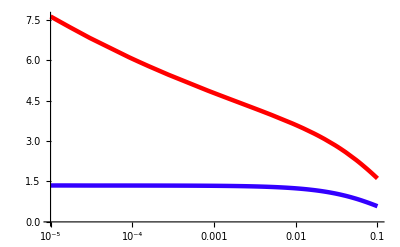

```mathematica
LogLinearPlot[{x gpdHzeroQ[x, 0, 4,4,P->0], gpdHzeroG[x, 0, 4,4,P->0]},{x,1*^-5,0.1},PlotStyle->{{Hue[0.7],Thickness[0.008]},{Hue[1],Thickness[0.008]}},PlotPoints->3]
```

```mathematica
PrintMinuitCommand["show correlations",12]
```

{}

This looks reasonable. Now, we fit to DVCS data, but first have to save parameters.

```mathematica
SaveParameters[]
```

## 3. DVCS fit (LO, nl-SO3)

```mathematica
GepardFit[{M02S,SECS,SECG},P->0,DATFILE->"dvcs",OUTFILE->"nlo-LO-DVCS"]
```

17.06431

Quality of covariance matrix = 3

----    Total and partial chi-squares  -----

|     total      | part-1 | part-2 | part-3
χ^2 | 95.9 | 53.2 | 27.0 | 15.8
d.o.f | 98 | 56 | 29 | 16
probabilities | 0.541 | 0.583 | 0.572 | 0.470

----    Parameter status :       -----

14 | M02S | 1. | 0.1 | 0. | 0. | 0.478391 | 0.0280999 | 1
17 | SECS | 0. | 0.1 | 0. | 0. | -0.15152 | 0.00697934 | 2
27 | SECG | 0. | 0.1 | 0. | 0. | -0.81217 | 0.0425155 | 3

```mathematica
SaveParameters[]
```

```mathematica
PrintMinuitCommand["show correlations",12, "nlo-LO-DVCS"]; (* evaluate twice to get output*)
```

**   35 **CALI    3.000    
 **********
 -----    Gepard parameters:    -----
 SPEED = 1     P = 0     NF = 4
 SCHEME = CSBAR   Q02 =   4.0
EndOfFile

```mathematica
PrintMinuitCommand["show correlations",12, "nlo-LO-DVCS"];
```

**   36 **SHOW CORRELATIONS 
 **********
 PARAMETER  CORRELATION COEFFICIENTS
       NO.  GLOBAL    14    17    27
       14  0.90097  1.000-0.580-0.467
       17  0.88554 -0.580 1.000-0.321
       27  0.86356 -0.467-0.321 1.000
EndOfFile

```mathematica
Epars  = Parameters;
```

## 4. Evaluation of CFFs ℋ and ℰ

For old models  (FIT and FITEXP),  κ_S and κ_G are independent parameters. E.g., if one sets κ_G=κ_S  then ℋ and ℰ become proportional

```mathematica
SetParameterValue[KAPS, 0.8];
SetParameterValue[KAPG, 0.8];
```

```mathematica
Abs[cffE[1.*^-4,-0.25,2.5,2.5,P->0]]/Abs[cffH[1.*^-4,-0.25,2.5,2.5,P->0]]
```

0.8

Sum rule  κ_G(0.6-N_S)=-κ_S N_S   is  valid for  new models  EPH, EPHEXP, EFL, and EFLEXP. In particular, for EPH (EPHEXP) models, whe have:

E_S=κ_s H_S

E_G=-(κ_(s N_S))/(0.6-N_S) ℋ_G

```mathematica
gpdEtrajQ[0.01, 0., 4., 4., P->0, ANSATZ->"EPH"] ==GetParameterValue[KAPS]*gpdHtrajQ[0.01, 0., 4., 4., P->0, ANSATZ->"EPH"]
```

True

```mathematica
gpdEtrajG[0.01, 0., 4., 4., P->0, ANSATZ->"EPH"] ==-(GetParameterValue[KAPS]GetParameterValue[NS])/(0.6-GetParameterValue[NS])*gpdHtrajG[0.01, 0., 4., 4., P->0, ANSATZ->"EPH"]
```

True

#### Dipole t-dependence

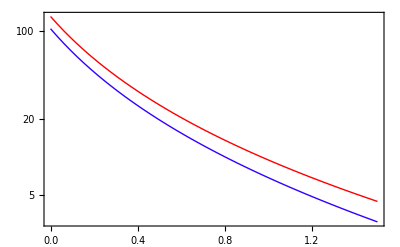

```mathematica
LogPlot[{Im[cffH[0.01,-tm,4.,4., P->0,ANSATZ->"EPH"]],Im[cffE[0.01,-tm,4.,4., P->0,ANSATZ->"EPH"]]},{tm,0.,1.5},PlotStyle->{Hue[1],Hue[0.7]},PlotRange->All, Frame->True]
```

We can now add additional t-dependence term  exp(ΔB t) which multiplies ℰ, like this:

```mathematica
SetParameterValue[DELB, 0.8]
```

0.8

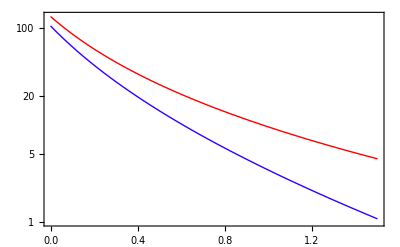

```mathematica
LogPlot[{Im[cffH[0.01,-tm,4.,4., P->0,ANSATZ->"EPH"]],Im[cffE[0.01,-tm,4.,4., P->0,ANSATZ->"EPH"]]},{tm,0.,1.5},PlotStyle->{Hue[1],Hue[0.7]},PlotRange->All, Frame->True]
```

#### Exponential t-dependence

```mathematica
SetParameterValue[ALPS, 0.];
SetParameterValue[ALPG, 0.];
SetParameterValue[M02S, 0.2];
SetParameterValue[M02G, 1/4.63];
```

```mathematica
SetParameterValue[DELB, 0.]
```

0.

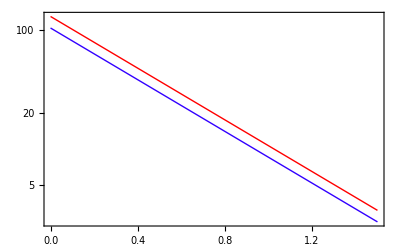

```mathematica
LogPlot[{Im[cffH[0.01,-tm,4.,4., P->0,ANSATZ->"EPHEXP"]],Im[cffE[0.01,-tm,4.,4., P->0,ANSATZ->"EPHEXP"]]},{tm,0.,1.5},PlotStyle->{Hue[1],Hue[0.7]},PlotRange->All, Frame->True]
```

```mathematica
SetParameterValue[DELB, 0.8]
```

0.8

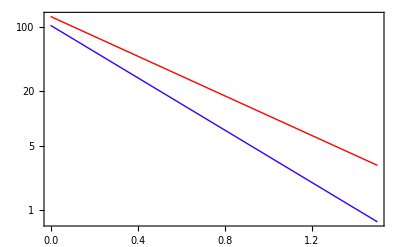

```mathematica
LogPlot[{Im[cffH[0.01,-tm,4.,4., P->0,ANSATZ->"EPHEXP"]],Im[cffE[0.01,-tm,4.,4., P->0,ANSATZ->"EPHEXP"]]},{tm,0.,1.5},PlotStyle->{Hue[1],Hue[0.7]},PlotRange->All, Frame->True]
```

## 5. DVCS fit with additional exp(ΔB t) parameter

We fit from the minimum of previous fit, and we see that we can slightly decrease the χ^2  95.9  → 95.1,  and errors on new parameters are large. We know that we are not sensitive to E with just H1/ZEUS data.

```mathematica
Parameters=Epars;
```

```mathematica
SetParameterValue[KAPS,0.5];
SetParameterValue[DELB,0.5];
```

```mathematica
GepardFit[{KAPS,DELB},P->0,DATFILE->"dvcs",OUTFILE->"new", ANSATZ->"EPH"]
```

5.10484

Quality of covariance matrix = 3

----    Total and partial chi-squares  -----

|     total      | part-1 | part-2 | part-3
χ^2 | 95.1 | 52.4 | 27.2 | 15.6
d.o.f | 99 | 56 | 29 | 16
probabilities | 0.591 | 0.613 | 0.563 | 0.481

----    Parameter status :       -----

18 | KAPS | 0.5 | 0.1 | 0. | 0. | 1.20952 | 0.82291 | 1
48 | DELB | 0.5 | 0.1 | 0. | 0. | 1.26296 | 1.39843 | 2

## 6. DVCS fit with flexible E

Full set of parameters for flexible E ansaetze  EFL and EFLEXP, we again start close to the minimum of original fit. Again, there is some decrease the χ^2  → 93.5.

```mathematica
Parameters=({{11, "NS", 0.15, 0.1, 0.0, 0.0}, {12, "AL0S", 1.15751, 0.1, 0.0, 0.0}, {13, "ALPS", 0.15, 0.1, 0.0, 0.0}, {14, "M02S", 0.478391, 0.1, 0.0, 0.0}, {15, "DELM2S", 0.0, 0.1, 0.0, 0.0}, {16, "PS", 2.0, 0.1, 0.0, 0.0}, {17, "SECS", -0.15152, 0.1, 0.0, 0.0}, {18, "KAPS", 1.21, 0.1, 0.0, 0.0}, {19, "SKEWS", 0.0, 0.1, 0.0, 0.0}, {22, "AL0G", 1.1, 0.1, 0.0, 0.0}, {23, "ALPG", 0.15, 0.1, 0.0, 0.0}, {24, "M02G", 0.7, 0.1, 0.0, 0.0}, {25, "DELM2G", 0.0, 0.1, 0.0, 0.0}, {26, "PG", 2.0, 0.1, 0.0, 0.0}, {27, "SECG", -0.81217, 0.1, 0.0, 0.0}, {28, "KAPG", 0.0, 0.1, 0.0, 0.0}, {29, "SKEWG", 0.0, 0.1, 0.0, 0.0}, {32, "THIS", 0.0, 0.1, 0.0, 0.0}, {42, "THIG", 0.0, 0.1, 0.0, 0.0}, {48, "DELB", 1.26, 0.1, 0.0, 0.0}, {112, "EAL0S", 1.15751, 0.1, 0.0, 0.0}, {113, "EALPS", 0.15, 0.1, 0.0, 0.0}, {114, "EM02S", 0.478391, 0.1, 0.0, 0.0}, {115, "EDELM2S", 0.0, 0.1, 0.0, 0.0}, {116, "EPS", 2.0, 0.1, 0.0, 0.0}, {117, "ESECS", -0.15152, 0.1, 0.0, 0.0}, {119, "ESKEWS", 0.0, 0.1, 0.0, 0.0}, {122, "EAL0G", 1.24732, 0.1, 0.0, 0.0}, {123, "EALPG", 0.15, 0.1, 0.0, 0.0}, {124, "EM02G", 0.7, 0.1, 0.0, 0.0}, {125, "EDELM2G", 0.0, 0.1, 0.0, 0.0}, {126, "EPG", 2.0, 0.1, 0.0, 0.0}, {127, "ESECG", -0.81217, 0.1, 0.0, 0.0}, {129, "ESKEWG", 0.0, 0.1, 0.0, 0.0}, {132, "ETHIS", 0.0, 0.1, 0.0, 0.0}, {142, "ETHIG", 0.0, 0.1, 0.0, 0.0}});
```

```mathematica
JustCali3[{},P->0,DATFILE->"dvcs",OUTFILE->"new",ANSATZ->"EFL"]
```

χ^2 = 138.416

```mathematica
GepardFit[{M02S, SECS,SECG,DELB,EAL0S,EM02S, ESECS},P->0,DATFILE->"dvcs",OUTFILE->"new",ANSATZ->"EFL"]
```

59.883399

Quality of covariance matrix = 3

----    Total and partial chi-squares  -----

|     total      | part-1 | part-2 | part-3
χ^2 | 93.5 | 46.7 | 29.9 | 16.9
d.o.f | 94 | 56 | 29 | 16
probabilities | 0.495 | 0.808 | 0.417 | 0.393

----    Parameter status :       -----

14 | M02S | 0.478391 | 0.1 | 0. | 0. | 0.478391 | 1.41421 | 1
17 | SECS | -0.15152 | 0.1 | 0. | 0. | -0.221826 | 0.0220796 | 2
27 | SECG | -0.81217 | 0.1 | 0. | 0. | -0.781265 | 0.0823665 | 3
48 | DELB | 1.26 | 0.1 | 0. | 0. | 1.12666 | 0.440861 | 4
112 | EAL0S | 1.15751 | 0.1 | 0. | 0. | 1.21154 | 0.0244908 | 5
114 | EM02S | 0.478391 | 0.1 | 0. | 0. | 0.449238 | 0.0600072 | 6
117 | ESECS | -0.15152 | 0.1 | 0. | 0. | 0.215973 | 0.145763 | 7

```mathematica
PrintMinuitCommand["show correlations",12, "new"]; (* evaluate twice to get output*)
```

**   31 **CALI    3.000    
 **********
 -----    Gepard parameters:    -----
 SPEED = 1     P = 0     NF = 4
 SCHEME = CSBAR   Q02 =   4.0
EndOfFile

```mathematica
PrintMinuitCommand["show correlations",12, "new"];
```

**   32 **SHOW CORRELATIONS 
 **********
 PARAMETER  CORRELATION COEFFICIENTS
       NO.  GLOBAL    14    17    27    48   112   114   117
       14  0.00000  1.000 0.000 0.000 0.000 0.000 0.000 0.000
       17  0.98901  0.000 1.000-0.114-0.221-0.755-0.120 0.076
       27  0.95477  0.000-0.114 1.000-0.355-0.337-0.718 0.660
       48  0.95630  0.000-0.221-0.355 1.000 0.027 0.771 0.140
      112  0.99370  0.000-0.755-0.337 0.027 1.000 0.191-0.657
      114  0.98418  0.000-0.120-0.718 0.771 0.191 1.000-0.361
      117  0.98621  0.000 0.076 0.660 0.140-0.657-0.361 1.000
EndOfFile

```mathematica
SaveParameters[]
```

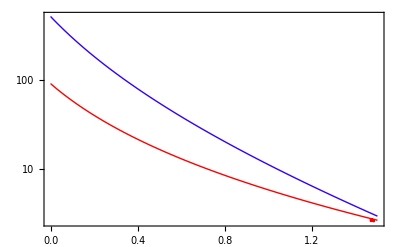

```mathematica
LogPlot[{Im[cffH[0.01,-tm,4.,4., P->0,ANSATZ->"EFL"]],Im[cffE[0.01,-tm,4.,4., P->0,ANSATZ->"EFL"]]},{tm,0.,1.5},PlotStyle->{Hue[1],Hue[0.7]},PlotRange->All, Frame->True]
```

## 7. Misc

```mathematica
<<expfits.m
```

```mathematica
Parameters = EIC12;
```

```mathematica
QS2=5/18;
```

```mathematica
Im[cffH[0.001,-0.2,4,4,P->0, ANSATZ->"EFLEXP"]]
```

848.162

```mathematica
1/(π QS2)Im[cffH[0.001,-0.2,4,4,P->0, ANSATZ->"EFLEXP"]]
```

971.922

```mathematica
gpdHtrajQ[0.001, -0.2,4,4,P->0, ANSATZ->"EFLEXP"]
```

971.922

```mathematica
gpdHtrajG[0.001, -0.2,4,4,P->0, ANSATZ->"EFLEXP"]
```

2.25627

```mathematica
gpdEtrajQ[0.001, -0.2,4,4,P->0, ANSATZ->"EFLEXP"]
```

1564.89

```mathematica
gpdEtrajG[0.001, -0.2,4,4,P->0, ANSATZ->"EFLEXP"]
```

-1.20967